CHAPTER ChapterLabel

Audio and Music Processing

Deep in the back of my mind is an unrealized sound
Every feeling I get from the street says it soon
could be found
When I hear the cold lies of the pusher,
I know it exists
It’s confirmed in the eyes of the kids, emphasized
with their fists
...
The music must change
For we’re chewing a bone
We soared like the sparrow hawk flied
Then we dropped like a stone
Like the tide and the waves
Growing slowly in range
Crushing mountains as old as the Earth
So the music must change

The Who, “Music Must Change”

ChapterLabel.Heading1  Introduction

Audio and music can be approached in three different ways with Mathematica:
(1) as traditional musical notes with associated pitch names and other specifications, such as duration, timbre, loudness, etc.; (2) as abstract mathematical waveforms that  represent vibrating systems; and (3) as digitally represented sound—just think of .wav and .aiff files. If nothing else, this chapter should hint at the ease with which Mathematica can be put in the service of the arts. Let’s make some music!

Mathematica allows you to approach music and sound in at least three different ways. You can talk to Mathematica about musical notes such as "C" or "Fsharp". You can directly specify other traditional concepts, such as timbre and loudness, with Mathematica’s Sound, SoundNote, and PlayList functions. You can ask Mathematica to play analog waveforms. And you can ask Mathematica to interpret digital sound samples.

ChapterLabel.Heading1  Creating Musical Notes

Problem

You want to create musical notes corresponding to traditional musical notation.

Solution

The Mathematica function SoundNote represents a musical sound. SoundNote uses either a numerical convention, for which middle C is represented as zero, or it accepts strings like "C", "C3", or "Aflat4", where "A0" represents the lowest note on a piano keyboard.

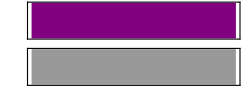

```mathematica
Sound[SoundNote[0]]
```

```mathematica
Sound[SoundNote["C"]]
```

-Graphics-

Discussion

SoundNote assumes you want to play a piano sound, for exactly one second, at a medium volume. You can override these presets. Here’s a loud (SoundVolume→1), short (0.125 second), guitar blast ("GuitarOverdriven").

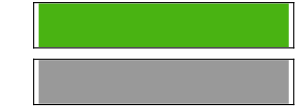

```mathematica
Sound[SoundNote[0,0.125,"GuitarOverdriven",SoundVolume->1]]
```

ChapterLabel.Heading1  Creating a Scale or a Melody

Problem

You want to create a sequence of notes, like a scale or single-note melody.

Solution

Sound can accept a list of notes, which it will play sequentially. Here is a whole-tone scale specified to take exactly 1.5 seconds to play in its entirety.

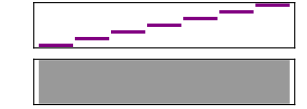

```mathematica
Sound[{SoundNote[0],SoundNote[2],SoundNote[4],SoundNote[6],SoundNote[8],SoundNote[10],SoundNote[12]},1.5]
```

Here’s an alternative syntax using Map (/@), which requires less typing and collects the note specifications into a list.

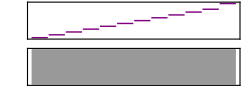

```mathematica
Sound[SoundNote[#]& /@ {0,2,4,6,8,10,12,14,16,18,20,24},1.0]
```

Here’s a randomly generated melody composed of notes from an A♭ major scale. The duration of each note is specified as 0.125 second. The duration specification, now a parameter of SoundNote rather than an overall specification of the entire melody as in the previous examples, sets the stage for the next example.

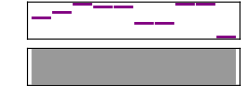

```mathematica
Sound[SoundNote[#, 0.125]& /@ RandomChoice[{"Aflat2","Bflat2","C3","Dflat3","Eflat3","F3","G3","Aflat3"},10]]
```

ChapterLabel.Heading1  Adding Rhythm to a Melody

Problem

You need to specify a melody for which the notes have different rhythm values.

Solution

Replace the 0.125 specification in the previous example with other values. Since you’re generating a random melody, why not generate random durations?

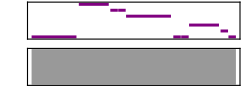

```mathematica
Sound[SoundNote[#, RandomChoice[{0.125,0.5,0.75,1.0}]]& /@ RandomChoice[{"Aflat2","Bflat2","C3","Dflat3","Eflat3","F3","G3","Aflat3"},10]]
```

Here, the weighting feature of RandomChoice is used to guarantee a preponderance of short notes.

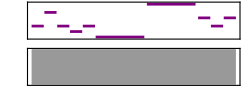

```mathematica
Sound[SoundNote[#, RandomChoice[{10,1,1,1}-> {0.125,0.5,0.75,1.0}]]& /@ RandomChoice[{"Aflat2","Bflat2","C3","Dflat3","Eflat3","F3","G3","Aflat3"},10]]
```

ChapterLabel.Heading1  Controlling the Volume

Problem

You would like to add some phrasing to your melody by controlling the volume.

Solution

Unlike duration, which is specified as a parameter to SoundNote, you control the volume with an option setting. Pulling everything together from the examples above

and adding a randomized volume yields this funky guitar pattern. Anyone for a cup of Maxwell House coffee?

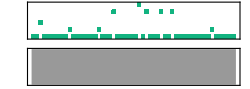

```mathematica
Sound[SoundNote[#, 0.125,"GuitarMuted",SoundVolume->RandomReal[]]& /@ RandomChoice[{20,1,1,1,1,1}-> {0,2,4,7,9,12},56]]
```

ChapterLabel.Heading1  Creating Chords

Problem

You want to move beyond simple sequences of single notes to chord patterns.

Solution

To make a chord, give SoundNote a list of notes. For example, you can specify the C major triad using the pitches C, E, and G specified as a list of numbers {0,4,7}. Don’t confuse making chords by giving SoundNote a list of notes with making melodies by giving Sound a list of SoundNotes.

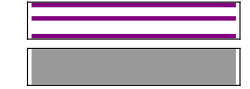

```mathematica
Sound[SoundNote[{0,4,7}]]
```

ChapterLabel.Heading1  Playing a Chord Progression

Problem

You want to make a chord progression.

Solution

This is the same as making melodies. Spell out the chords in your chord progression as lists inside a list. Feed them into SoundNote using Map.

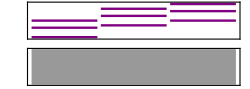

```mathematica
Sound[SoundNote[#,0.5]& /@ {{"C3","E3","G3"},{"F3","A3","C4"},{"G3","B3","D4"}}]
```

Here’s a popular pop song progression.

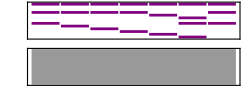

```mathematica
Sound[SoundNote[#,1]& /@ {{"C3","E3","G3"},{"B2","E3","G3"},{"Bb2","E3","G3"},{"A2","E3","G3"},{"Aflat2","Eflat3","G3"},{"G2","C3","D3","G3"},{"C3","E3","G3"}}]
```

ChapterLabel.Heading1  Writing Music with Traditional 
Chord Notation

Problem

You want to specify a chord progression using traditional notation. For example, you would like to write something like:

```mathematica
myProg="C A7 d-7 F/G C";
```

or, using roman numerals as is common in jazz notation,

```mathematica
myJazzProgression="<Eb>   I vi-9 II7/#9b13 ii-9 V7sus I";
```

Solution

Mathematica can deftly handle this task with its String manipulation routines and its pattern recognition functions. First, decide which chord symbols will be allowed. Here’s a list of jazz chords: Maj7/9, Majadd9, add9, Maj7#11, Maj7/13, Maj7/#5, Maj7, Maj, -7b5, -7, -9, -11, min, 7/b913, 7/#9b13, 7/b9b13, 7/b9#11, 7/b5, 7/b9, 7/#9, 7/#11, 7/13, 7, 7/9, 7sus, and sus.

The rules below turn the chord names into the appropriate scale degree numbers in the key of C. Later, as a second step, you’ll transpose these voicings to other keys.

```mathematica
chordSpellingRules={"Maj7/9":>{0,4,7,11,14},"Majadd9":>{0,2,4,7},"add9":>{0,2,4,7},"Maj7/#11":>{0,4,7,11,14,18},"Maj7/13":>{2,6,9},"Maj7/#5":>{4,8,11},"Maj7":>{0,4,7,11},
"Maj":>{0,4,7},
(*lstead - added rule so "F" works*)
"" :> {0,4,7}, 
"-7b5":>{0,3,6,10},"-7":>{0,3,7,10},"-9":>{0,3,7,10,14},"-11":>{0,3,7,10,14,17},
"min":>{0,3,7},
(*lstead - added rule so "D-" works*)
"-" :> {0,3,7},
"7/b913":>{1,4,9,10},"7/#9b13":>{0,3,8},"7/b9b13":>{1,4,8,10},"7/b9#11":>{1,4,6,10},"7/b5":>{0,4,6,10},
"7/b9":>{1,4,7,10},"7/#9":>{4,10,15},"7/#11":>{0,4,7,10,14,18},"7/13":>{4,9,10,14},"7":>{0,4,7,10},"7/9":>{0,4,7,10,14},"7sus":>{0,5,7,10},"sus":>{0,5,7,12}};
```

```mathematica
romanRoots = {"bIII":>3,"III":>4,"bII":>1,"II":>2,"#II":>3,"IV":>5,"#IV":>6,"bVII":>10,"VII":>11,"bVI":>8,"VI":>9,"#VI":>10,"bV":>6,"V":>7,"#V":>8,"I":>0,"#I":>1}; letterRoots = {"C":>0,"C#":>1,"Db":>1,"D":>2,"D#":>3,"Eb":>3,"E":>4,"F":>5,"F#":>6,"Gb":>6,"G":>7,"G#":>8,"Ab":>8,"A":>9,"Bb":>10,"B":>11};
roots = Join[romanRoots, letterRoots]
```

{bIII:>3,III:>4,bII:>1,II:>2,#II:>3,IV:>5,#IV:>6,bVII:>10,VII:>11,bVI:>8,VI:>9,#VI:>10,bV:>6,V:>7,#V:>8,I:>0,#I:>1,C:>0,C#:>1,Db:>1,D:>2,D#:>3,Eb:>3,E:>4,F:>5,F#:>6,Gb:>6,G:>7,G#:>8,Ab:>8,A:>9,Bb:>10,B:>11}

Make a table by concatenating together each possible root and type. Then /. can be used to decode chord.

```mathematica
compoundRules = Table[ToUpperCase[l⟦1,1⟧~~l⟦2,1⟧]->
{l⟦1,2⟧,l⟦2,2⟧},{l,Tuples[{roots, chordSpellingRules}]}];
drules = Dispatch[compoundRules];
```

Now create a function for converting the chord string into a progression representation.

```mathematica
progressionFromString[s_]:=
Block[{su,ss},
ss = StringSplit[s,Whitespace];
progression[First[ss], ToUpperCase[Rest[ss]]]]

progression[key_, chords_]:=
Block[{keyCenter, lh,rh},
keyCenter = StringCases[key,
RegularExpression["(?i)[a-z]+"]]⟦1⟧ /. letterRoots;
progression[key, chords,keyCenter,
Table[
{lh, rh} =(chord /. drules);
lh = lh +keyCenter -24;
rh = rh + lh + 24;
Flatten[{lh,rh}],
{chord, chords}]]]
```

And a function to play the progression.

```mathematica
playProgression[progression[k_, csyms_,kn_, chords_]]:=
Sound[SoundNote[#,1]&/@chords,5]
```

Let’s test it on a jazz progression.

```mathematica
jazzS = "<Eb>   I vi-9 II7/#9b13 ii-9 V7sus I";
```

```mathematica
jazzP = progressionFromString[jazzS]
```

progression[<Eb>,{I,VI-9,II7/#9B13,II-9,V7SUS,I},3,{{-21,3,7,10},{-12,12,15,19,22,26},{-19,5,8,13},{-19,5,8,12,15,19},{-14,10,15,17,20},{-21,3,7,10}}]

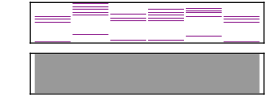

```mathematica
playProgression[jazzP]
```

Let’s add some rhythm and volume.

```mathematica
buffer = progressionFromString[jazzS][[4]]
Sound[MapIndexed[SoundNote[#,{1,0.5,0.5,0.75,0.25,1}⟦Sequence @@ #2⟧,SoundVolume->RandomReal[0.5,1]]&,buffer]]
```

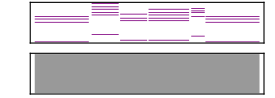

```mathematica
{{-21,3,7,10},{-12,12,15,19,22,26},{-19,5,8,13},{-19,5,8,12,15,19},{-14,10,15,17,20},{-21,3,7,10}}
```

Discussion

There’s a very unsatisfying feature to the result: the chords jump around in an unmusical way. A piano player would typically invert the chords to keep the voicings centered around middle C. So for example, when playing a CMaj7 chord, which is
defined as {0,4,7,11} or {"C3","E3","G3","B3"}, a piano player might drop the top two notes down an octave and play {-5,-1,0,4} or {"G2","B2","C3","E3"}. You can use Mathematica’s Mod function to achieve the same result. Here the notes greater than 6 {"F#3"} are transposed down an octave simply by subtracting 12 from them.

```mathematica
buffer
```

{{-21,3,7,10},{-12,12,15,19,22,26},{-19,5,8,13},{-19,5,8,12,15,19},{-14,10,15,17,20},{-21,3,7,10}}

Currently in the buffer, the nonbass notes are all positive, so this rule, which uses /; n>0 as a condition, leaves the (negative) bass notes untouched while processing the rest of the voicing.

```mathematica
buffer/.{n_Integer/;n>0:>Mod[n,12,-5]}
```

{{-21,3,-5,-2},{-12,0,3,-5,-2,2},{-19,5,-4,1},{-19,5,-4,0,3,-5},{-14,-2,3,5,-4},{-21,3,-5,-2}}

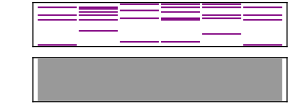

```mathematica
Sound[SoundNote[#,1]& /@( buffer/.{n_Integer/;n>0:>Mod[n,12,-5]})]
```

Here’s another progression showing all the steps in one place.

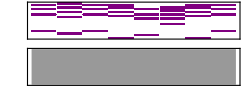

```mathematica
buffer=progressionFromString["<F> F Eb7 F C7 d- Bb7 C7 F"][[4]];
Sound[SoundNote[#,1]& /@( buffer/.{n_Integer/;n>0:>Mod[n,12,-5]})]
```

ChapterLabel.Heading1  Creating Percussion Grooves

Problem

You want to make percussion sounds.

Solution

Mathematica has implemented 60 percussion instruments as specified in the General MIDI (musical instrument digital interface) specification.

Here the percussion instruments are listed in alphabetical order. Some of the names are not obvious. For example, there is no triangle or conga, instead there’s "MuteTriangle", "OpenTriangle", "HighCongaMute", "HighCongaOpen", and "LowConga".

```mathematica
allPerc={"BassDrum","BassDrum2","BellTree","Cabasa","Castanets","ChineseCymbal","Clap","Claves","Cowbell","CrashCymbal","CrashCymbal2","ElectricSnare","GuiroLong","GuiroShort","HighAgogo","HighBongo","HighCongaMute","HighCongaOpen","HighFloorTom","HighTimbale","HighTom","HighWoodblock","HiHatClosed","HiHatOpen","HiHatPedal","JingleBell","LowAgogo","LowBongo","LowConga","LowFloorTom","LowTimbale","LowTom","LowWoodblock","Maracas","MetronomeBell","MetronomeClick","MidTom","MidTom2","MuteCuica","MuteSurdo","MuteTriangle","OpenCuica","OpenSurdo","OpenTriangle","RideBell","RideCymbal","RideCymbal2","ScratchPull","ScratchPush","Shaker","SideStick","Slap","Snare","SplashCymbal","SquareClick","Sticks","Tambourine","Vibraslap","WhistleLong","WhistleShort"};
```

Here’s what each instrument sounds like. The instrument name is fed into SoundNote where, more typically, the note specification should be. In fact, in the Standard MIDI specification, each percussion instrument is represented as a single pitch in a “drum” patch. So for example, "BassDrum" is C0, "BassDrum2" is C#0, "Snare" is D0, and so on. Therefore, it makes sense for Mathematica to treat these instruments as notes, not as “instruments” as was done above for "Piano", "GuitarMuted", and "GuitarOverDriven".

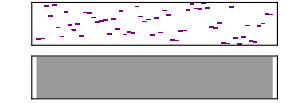

```mathematica
Sound[SoundNote[#,0.125]&/@ allPerc]
```

Here’s a measure’s worth of closed hi-hat:

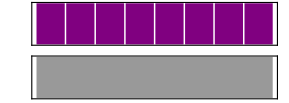

```mathematica
Sound[SoundNote[#,0.125]&/@ Table["HiHatClosed",{8}]]
```

And here’s something with a little more pizzazz. Both the choice of instrument and volume are randomized.

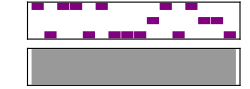

```mathematica
Sound[SoundNote[#,0.125,SoundVolume->RandomReal[{0.25,1}]]& /@ Table[RandomChoice[{"HiHatOpen","HiHatClosed","HiHatPedal"}],{16}]]
```

ChapterLabel.Heading1  Creating More Complex Percussion Grooves

Problem

You want to create a drum kit groove for a pop song using kick, snare, and hi-hat.

Solution

This task is the percussion equivalent of making chords, because on certain beats all three instruments could be playing, on other beats only one instrument or possibly none. Here’s the previous hi-hat pattern, played at a slower tempo.

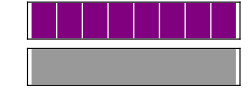

```mathematica
Sound[SoundNote[#,0.25]&/@ Table["HiHatClosed",{8}]]
```

Here’s a kick drum pattern. Use None as a rest indication.

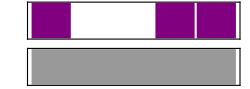

```mathematica
Sound[SoundNote[#,0.25]&/@ {"BassDrum",None,None,"BassDrum","BassDrum",None,None,None}]
```

Here’s the snare drum backbeat. The display omits the leading rests, so the picture is a little misleading. As soon as we integrate this with the hi-hat and kick drum,
everything will look correct.

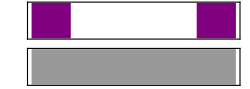

```mathematica
Sound[SoundNote[#,0.25]&/@ {None,None,"Snare",None,None,None,"Snare",None}]
```

Each list has exactly eight elements, so we can use Transpose to interlace the elements.

```mathematica
groove=Transpose[{Table["HiHatClosed",{8}],{"BassDrum",None,None,"BassDrum","BassDrum",None,None,None},{None,None,"Snare",None,None,None,"Snare",None}}]
```

{{HiHatClosed,BassDrum,None},{HiHatClosed,None,None},{HiHatClosed,None,Snare},{HiHatClosed,BassDrum,None},{HiHatClosed,BassDrum,None},{HiHatClosed,None,None},{HiHatClosed,None,Snare},{HiHatClosed,None,None}}

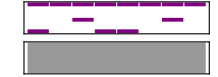

```mathematica
Sound[SoundNote[#,0.25]&/@ groove]
```

An entire tune can now be made by repeating this one-measure groove as many times as desired.

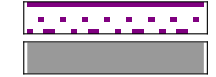

```mathematica
Sound[SoundNote[#,0.25]&/@ Flatten[Table[ groove,{4}],1]]
```

Discussion

Getting the curly braces just right in Mathematica’s syntax can be a little frustrating. Without Flatten in the example above, the SoundNote function is confused by the List-within-List results of the Table function. Consequently, you get no output.

```mathematica
Sound[SoundNote[#,0.25]&/@ Table[ groove,{4}]]
```

```mathematica
Sound[{SoundNote[{{"HiHatClosed","BassDrum",None},{"HiHatClosed",None,None},{"HiHatClosed",None,"Snare"},{"HiHatClosed","BassDrum",None},{"HiHatClosed","BassDrum",None},{"HiHatClosed",None,None},{"HiHatClosed",None,"Snare"},{"HiHatClosed",None,None}},0.25],SoundNote[{{"HiHatClosed","BassDrum",None},{"HiHatClosed",None,None},{"HiHatClosed",None,"Snare"},{"HiHatClosed","BassDrum",None},{"HiHatClosed","BassDrum",None},{"HiHatClosed",None,None},{"HiHatClosed",None,"Snare"},{"HiHatClosed",None,None}},0.25],
```

```mathematica
SoundNote[{{"HiHatClosed","BassDrum",None},{"HiHatClosed",None,None},{"HiHatClosed",None,"Snare"},{"HiHatClosed","BassDrum",None},{"HiHatClosed","BassDrum",None},{"HiHatClosed",None,None},{"HiHatClosed",None,"Snare"},{"HiHatClosed",None,None}},0.25],SoundNote[{{"HiHatClosed","BassDrum",None},{"HiHatClosed",None,None},{"HiHatClosed",None,"Snare"},{"HiHatClosed","BassDrum",None},{"HiHatClosed","BassDrum",None},{"HiHatClosed",None,None},{"HiHatClosed",None,"Snare"},{"HiHatClosed",None,None}},0.25]}]
```

Furthermore, with a simple Flatten wrapped around the Table function, each hit is treated individually; we lose the chordal quality of the drums hitting simultaneously. Go back and notice that the correct idea is to remove just one layer of braces by using Flatten[ ... , 1 ].

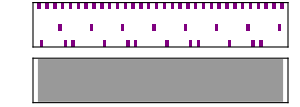

```mathematica
Sound[SoundNote[#,0.25]&/@ Flatten[Table[ groove,{4}]]]
```

ChapterLabel.Heading1  Exporting MIDI files

Problem

You want to save your Mathematica expression as a standard MIDI file.

Solution

Mathematica can export any expression composed of Sound and SoundNote expressions as a standard MIDI file. The rub, however, is that Mathematica does not import MIDI files. So let’s create some utilities that at the very least let you look at the guts of standard MIDI files.

Here’s a simple phrase that gets exported as the file myPhrase.mid.

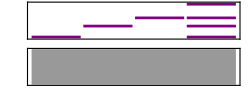

```mathematica
myPhrase=Sound[{SoundNote[0],SoundNote[4],SoundNote[7],SoundNote[{0,4,7,12}]}]
```

```mathematica
Export["myPhrase.mid",myPhrase]
```

myPhrase.mid

ChapterLabel.Heading1  Playing Functions As Sound

Problem

You want to listen to the waveform generated by a mathematical function.

Solution

If you know how to plot a function in Mathematica:

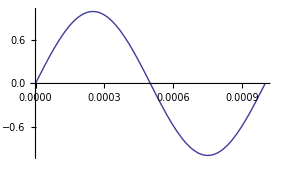

```mathematica
Plot[Sin[1000*2π*t],{t,0,0.001},ImageSize->300]
```

You can play a function. Play uses the same syntax as Plot. However, you don’t want to listen to 1/1000th of a second, which is what was plotted above, so specify something like {t, 0, 1}.

```mathematica
Play[Sin[1000*2π*t],{t,0,1}]
```

-Graphics-

Discussion

Here are other crazy-sounding functions.

```mathematica
Play[Sin[300  2 π  t Exp[t]], {t,0,8}]
```

-Graphics-

```mathematica
Play[(2+Cos[40t^2])Sin[700t^2],{t,0,10}]
```

-Graphics-

ChapterLabel.Heading1  Adding Tremolo

Problem

You want to add tremolo.

Solution

“Tremolo” is the musical term for amplitude modulation. Here a 20 Hz signal modifies the amplitude of a 1,000 Hz signal.

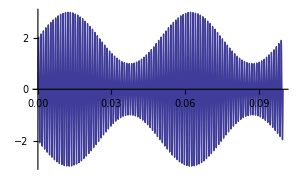

```mathematica
Plot[(2+Sin[20*2π*t])*Sin[1000*2π*t],{t,0,0.1},ImageSize->300]
```

And here, a 5 Hz signal modifies a 1,000 Hz signal.

```mathematica
Play[(2+Sin[5*2π*t])*Sin[1000*2π*t],{t,0,1}]
```

-Graphics-

ChapterLabel.Heading1  Adding Vibrato

Problem

You want to add vibrato.

Solution

Vibrato is frequency modulation. Notice that the sine wave alternates between regions of compression and expansion.

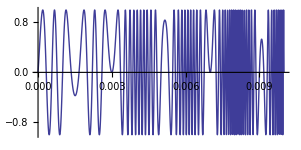

```mathematica
Plot[(Sin[(1+Sin[250*2π*t])*1000*2π*t]),{t,0,0.010},ImageSize->400,AspectRatio->0.5]
```

Here the parameters are adjusted for listening.

```mathematica
Play[(Sin[(1+0.002Sin[5*2π*t])*1000*2π*t]),{t,0,1}]
```

-Graphics-

Why not put the two modulations together: tremolo and vibrato?

```mathematica
Play[(2+Sin[5*2π*t])*Sin[(1+0.002Sin[5*2π*t])*1000*2π*t],{t,0,1}]
```

-Graphics-

ChapterLabel.Heading1  Applying an Envelope to a Signal

Problem

You want to apply an envelope to your signal.

Solution

The Mathematica function Piecewise is the perfect tool for creating an envelope. Here is the popular attack-decay-sustain-release (ADSR) envelope.

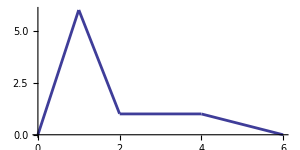

```mathematica
Plot[Piecewise[{
{6t,t<1},
{6-5(t-1),t<2},
{1,t<4},
{1-0.5(t-4),t<6}
}],
{t,0,6},
PlotStyle->AbsoluteThickness[2],ImageSize->{300,150},AspectRatio->0.5
]
```

Sine waves are typically represented as amplitude * sine (ωt). You can simply substitute the entire Piecewise[] envelope for amplitude.

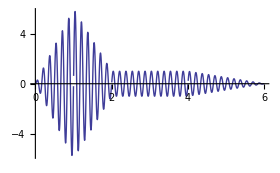

```mathematica
Plot[
Piecewise[{
{6t,t<1},
{-5(t-1)+6,t<2},
{1,t<4},
{-0.5(t-4)+1,t<6}}
]*Sin[6*2π*t],
{t,0,6},
PlotRange->All
]
```

Listen!

```mathematica
Play[
Piecewise[{
{(6t),t<1},
{(-5(t-1)+6),t<2},
{(1),t<4},
{(-0.5(t-4)+1),t<6}
}]*Sin[1000*2π*t],
{t,0,6}
]
```

-Graphics-

Discussion

Calculating the envelope functions for the four regions is not as hard as you might
expect. Perhaps you remember the equation for a straight line: y = m x + b, where m is the slope of the line and b is the y-intercept. Here is a line with a slope of –2 that
intercepts the y-axis at y = 4, so its equation is y = –2x + 4.

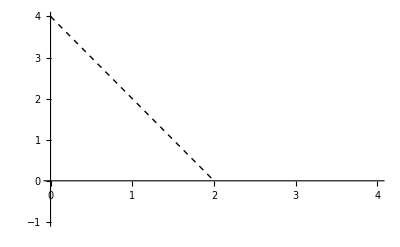

```mathematica
Plot[-2x+4,{x,0,2},PlotRange->{{0,4},{-1,4}},PlotStyle->{AbsoluteDashing[{4,4}],{Thick,Black}}]
```

If this were the function for the second portion of the envelope, the decay portion, you would need to shift this line to the right. You can shift the line to the right simply by replacing x with (x – displacement). In general, the template for creating the equations for the Piecewise functions will be: y = m (x – displacement) + initial value of segment. Notice that what was at first the y-intercept is now the “initial value of the segment.” The line here is shifted two units to the right, and the new equation is y = –2 (x – 2) + 4. If we simplify the right side, the equation becomes y = –2x + 8. This line has the same –2 slope but would intercept the y-axis at y = 8 if we were to extend the line to the left.

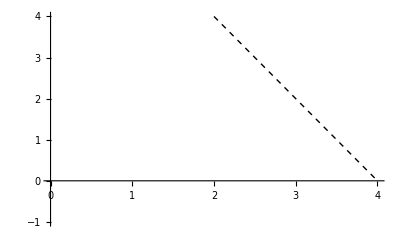

```mathematica
Plot[-2(x-2)+4,{x,0,4},PlotRange->{{0,4},{-1,4}},PlotStyle->{AbsoluteDashing[{4,4}],{Thick,Black}}]
```

ChapterLabel.Heading1  Exploring Alternate Tunings

Problem

You want to explore different partitions of the musical scale and alternate instrument tunings.

Solution

Modern Western music uses tempered tuning, which is a slight compromise to the vibrations of the natural world, or at least the perfection of the natural world as the Greeks described it 3,000 years ago. The ancient Greeks (and even earlier, the Babylonians) noticed that when objects vibrate in simple, integer ratios to each other, the
resulting sound is pleasant. The simple ratio of 2:1 is so pleasant that we perceive it
as an equivalence. When two notes vibrate in a ratio of 2:1, we say they have the same pitch but are in different octaves. The history of music has been the history of partitioning the octave.

The first obvious division of the octave is created by the next simplest ratio, a 3:1 ratio. Consider the following schematic of a vibrating string. The only requirement on the string is that its endpoints remain fixed. The string can vibrate in many different modes, as shown in the first column. Each mode has a characteristic number of still points, called “nodes,” that appear symmetrically along the length of the string. Each mode also has a characteristic rate of vibration, which is a simple integer multiple to the lowest fundamental frequency. Notice that three out of the first four harmonics are octave equivalences. The third harmonic, situated between the second and fourth harmonics, has a ratio of 3:2 to the second harmonic and 3:4 to the fourth. These were the kinds of simple ratios that appealed to the Greeks.

```mathematica
SetOptions[Plot,ImageSize->{150,30},AspectRatio->0.2,Ticks->None,PlotStyle->AbsoluteThickness[2]];
Style[Grid[{
{"mode","harmonic","musical interpretation","ratio to fundamental"},

{Plot[Sin[400 2π*t],{t,0,0.005}],"4th", "octave","4/1"},
{Plot[Sin[300 2π*t],{t,0,0.005}],"3rd", "fifth","3/1"},
{Plot[Sin[200 2π*t],{t,0,0.005}],"2nd", "octave","2/1"},
{Plot[Sin[100 2π*t],{t,0,0.005},PlotRange->{-1,1}],"1st", "tonic","1"}
},
Frame->All,
Background->{White,{White,White,White,White,White}}
],14,"Label"
]
```

mode | harmonic | musical interpretation | ratio to fundamental
-Graphics- | 4th | octave | 4/1
-Graphics- | 3rd | fifth | 3/1
-Graphics- | 2nd | octave | 2/1
-Graphics- | 1st | tonic | 1

mode | harmonic | musical interpretation | ratio to fundamental
-Graphics- | 4th | octave | 4/1
-Graphics- | 3rd | fifth | 3/1
-Graphics- | 2nd | octave | 2/1
-Graphics- | 1st | tonic | 1

mode | harmonic | musical interpretation | ratio to fundamental
-Graphics- | 4th | octave | 4/1
-Graphics- | 3rd | fifth | 3/1
-Graphics- | 2nd | octave | 2/1
-Graphics- | 1st | tonic | 1

The following keyboard shows how a successive application of the 3:2 ratio can be used to build the entire chromatic scale. After 12 applications of this 3:2 ratio, every note of the modern chromatic scale has been visited once and we are returned to starting pitch—sort of!

```mathematica
With[{y1=-1.6,y2=6.5},whiteKeys=Table[Rectangle[{x,0},{x+1,5}],{x,0,49}];
blackKeys=Table[Rectangle[{octave+x+0.65,2},{octave+x+1.3,5}],{x,{0,1,3,4,5}},{octave,0,42,7}];
sequential=Sort[Flatten@Join[whiteKeys,blackKeys]];
highlights=sequential⟦Table[n,{n,1,85,7}]⟧;
keyboard={White,EdgeForm[{Black,AbsoluteThickness[1]}],whiteKeys,Gray,highlights,Black,blackKeys,Gray,highlights⟦7;;11⟧};
Graphics[{keyboard,
Style[{Text["1",{0.5,y1}],Text[3/2,{4.5,y1}],Text[(3/2)^2,{8.5,y1}],Text[(3/2)^3,{12.5,y1}],Text[(3/2)^4,{16.5,y1}],
Text[(3/2)^5,{20.5,y1}],Text[(3/2)^6,{25,y2}],Text[(3/2)^7,{29,y2}],Text[(3/2)^8,{33,y2}],Text[(3/2)^9,{37,y2}],Text[(3/2)^10,{41,y2}],
Text[(3/2)^11,{45.5,y1}],Text[(3/2)^12,{49.5,y1}]},9]
},ImageSize->{550,200}]]
```

There’s a problem: (3/2)^12 represents the C seven octaves above the starting C and should equal a C with a frequency ratio of 2^7 = 128, but (3/2)^12 equals 129.75. The equal temperament solution to this problem is to distribute this discrepancy equally over all the intervals. In other words, in equal temperament, every interval is made slightly, and equally, “out of tune.” Johann Sebastian Bach composed a series of keyboard pieces in 1722 called “The Well-Tempered Clavier” to demonstrate that this compromise was basically imperceptible and had no negative impact on the beauty of the music.

Mathematically, equal temperament means that the frequency of each pitch should have the same ratio to its immediate lower neighbor’s frequency. Call this ratio α. Then it must be the case that if a chromatic scale, which contains 12 pitches, takes
you from some frequency to twice that frequency, then α^12= 2. So the ratio of a semitone in equal temperament is 1.0596.

```mathematica
α=2.0^(1/12)
```

1.05946

1.05946

1.05946

However, now that we have the octave in perfect shape, every other interval is slightly “wrong”—or at least wrong according to the manner in which the Greeks were trying to make their intervals. So for example, a Pythagorean fifth, which is 3/2 = 1.5, is slightly flat in equal temperament (the musical interval of a fifth is composed of seven half-steps).

```mathematica
α^7
```

1.49831 ^7

```mathematica
1.498307
```

1.49831

Now that we’ve gone through the basics of tuning, how do you use Mathematica to explore alternate tunings?

Discussion

As explained above, tuning instruments in the modern Western world is based on dividing the octave into 12 equal segments. If the ratio of the semitone C to C# is called α, then the ratio of the octave from C3 to C4 is α^12 and should equal 2.0. Therefore you can calculate α to be the 12th root of 20.

```mathematica
α=2.0^(1/12)
```

1.05946

1.05946

1.05946

Here’s the equal-tempered chromatic scale, sometimes referred to as 12-TET (twelve-tone equal temperament):

```mathematica
TET=Table[Sin[440.0*α^n*2π*t],{n,0,12}]
```

{Sin[2764.6 t],Sin[2928.99 t],Sin[3103.16 t],Sin[3287.68 t],Sin[3483.18 t],Sin[3690.3 t],Sin[3909.74 t],Sin[4142.22 t],Sin[4388.53 t],Sin[4649.49 t],Sin[4925.96 t],Sin[5218.87 t],Sin[5529.2 t]}

{Sin[2764.6 t],Sin[2928.99 t],Sin[3103.16 t],Sin[3287.68 t],Sin[3483.18 t],Sin[3690.3 t],Sin[3909.74 t],Sin[4142.22 t],Sin[4388.53 t],Sin[4649.49 t],Sin[4925.96 t],Sin[5218.87 t],Sin[5529.2 t]}

{Sin[2764.6 t],Sin[2928.99 t],Sin[3103.16 t],Sin[3287.68 t],Sin[3483.18 t],Sin[3690.3 t],Sin[3909.74 t],Sin[4142.22 t],Sin[4388.53 t],Sin[4649.49 t],Sin[4925.96 t],Sin[5218.87 t],Sin[5529.2 t]}

```mathematica
Show[Play[#,{t,0,0.25}]& /@ TET]
```

-Graphics-

The equal-tempered major scale is

```mathematica
Show[Play[#,{t,0,0.25}]& /@ TET⟦1+{0,2,4,5,7,9,11,12}⟧]
```

ChapterLabel.Heading1  Importing Digital Sound Files

Problem

You want to import a digital sound file, for example, a WAV or AIFF file.

Solution

Mathematica imports many standard file formats. Both AIFF and WAV are in the list.

```mathematica
$ImportFormats
```

{3DS,ACO,AIFF,ApacheLog,AU,AVI,Base64,Binary,Bit,BMP,Byte,BYU,BZIP2,CDED,CDF,Character16,Character8,Complex128,Complex256,Complex64,CSV,CUR,DBF,DICOM,DIF,Directory,DXF,EDF,ExpressionML,FASTA,FITS,FLAC,GenBank,GeoTIFF,GIF,Graph6,GTOPO30,GZIP,HarwellBoeing,HDF,HDF5,HTML,ICO,Integer128,Integer16,Integer24,Integer32,Integer64,Integer8,JPEG,JPEG2000,JVX,LaTeX,List,LWO,MAT,MathML,MBOX,MDB,MGF,MMCIF,MOL,MOL2,MPS,MTP,MTX,MX,NB,NetCDF,NOFF,OBJ,ODS,OFF,Package,PBM,PCX,PDB,PDF,PGM,PLY,PNG,PNM,PPM,PXR,QuickTime,RawBitmap,Real128,Real32,Real64,RIB,RSS,RTF,SCT,SDF,SDTS,SDTSDEM,SHP,SMILES,SND,SP3,Sparse6,STL,String,SXC,Table,TAR,TerminatedString,Text,TGA,TIFF,TIGER,TSV,UnsignedInteger128,UnsignedInteger16,UnsignedInteger24,UnsignedInteger32,UnsignedInteger64,UnsignedInteger8,USGSDEM,UUE,VCF,WAV,Wave64,WDX,XBM,XHTML,XHTMLMathML,XLS,XML,XPORT,XYZ,ZIP}

Using the "Data" specification will save you the aggravation of decoding the syntax of the imported data. Don’t forget the semicolon, which prevents Mathematica from listing all the sample points. The easiest way to access a file is to type Import[ ], place your cursor between the empty brackets, choose File... from the Insert Menu, navigate in the dialog box to the file you want to open.

```mathematica
file =FileNameJoin[{NotebookDirectory[] ,"..","data","JCK_01.aif"}];
data=Flatten@Import[file,"Data"];
```

You’ll need to know the sample rate and whether this file is a mono or stereo, so do a second Import on the same file but specify "Options".

```mathematica
Import[file,"Options"]
```

{AudioChannels→1,AudioEncoding→Integer16,SampleRate→48000}

If you simply wanted to play the file, specify "Sound" as the second parameter.

```mathematica
snd=Import[file,"Sound"];
```

This returns a Sound object.

```mathematica
snd//Head
```

Sound

And can be played like so:

```mathematica
snd
```

-Graphics-

Discussion

Sound files can be huge, and as such, become difficult to work with.

```mathematica
Length[data]
```

1396853

Here’s a quick way to get an overview of a sound file. Mathematica is being asked to display every thousandth sample point. You can easily see there are a handful of bursts of energy.

```mathematica
SetOptions[ListLinePlot,ImageSize->{500,150},AspectRatio->0.25,PlotRange->All];
```

```mathematica
SetOptions[ListPlot,ImageSize->{500,150},AspectRatio->0.25,PlotRange->All];
```

```mathematica
ListLinePlot[data⟦1;;1396000;;1000⟧]
```

-Graphics-

Focus on the three wavelets between 900 and 1,300.

```mathematica
ListLinePlot[data⟦900000;;1300000⟧]
```

“Yes we can; yes we can; yes we can!”

```mathematica
Sound[SampledSoundList[data⟦900000;;1300000⟧,48000]]
```

-Graphics-

ChapterLabel.Heading1  Analyzing Digital Sound Files

Problem

You want to do a Fourier analysis on a sound file. Fourier analysis is a means of investigating the energy in a signal. Specifically, Fourier analysis will report on the
energy spectrum of a signal versus frequency. The mathematics behind Fourier analysis is quite sophisticated, but armed with just a few principles, you can put Mathematica’s Fourier tools to work for you.

Solution

Typically you’ll start with a digitized signal. The sampling rate will determine the highest frequency that can be investigated. This highest frequency is called the Nyquist frequency and is always exactly one half the sampling rate. For this “Yes we

can!” sample, which was digitized at 48 KHz, the highest frequency is 24 KHz. (It’s not coincidental that this frequency is slightly greater than the limits of human hearing.) Notice the plot is symmetric about the Nyquist frequency.

The number of sample points used in any analysis is also critical. Here exactly one second of audio, that is, 48,000 sample points, is being analyzed. The 48,000 points from the time domain yield 48,000 points in the frequency domain, but as you can see, the right side of the plot, between points 24,000 and 48,000, is just a mirror duplication of the points between 0 and 24,000. This is an artifact of the underlying mathematics, and there is no additional information in this half of the plot.

```mathematica
ListLinePlot[Abs[Fourier[data⟦900000;;900000+48000⟧]]]
```

-Graphics-

Since this is speech, you can focus on the first 2,000 points, which correspond to
frequencies 0 to 2,000 Hz. Later you’ll see that 2,000 points of a Fourier analysis doesn’t always mean frequencies 0 through 2,000 Hz. It does in this case because you started with 48,000 sample points in the time domain that equals the sampling rate and created a one-to-one relationship between data points and frequencies in the frequency domain. You can see that this speaker has four significant frequency resonances to his voice at approximately 150 Hz, 300 Hz, 490 Hz, and 700 Hz. These resonances are known as formants. Notice, the Ticks option customized the labeling of the x-axis.

```mathematica
ListLinePlot[Abs[Fourier[data⟦900000;;900000+48000⟧]]⟦1;;2000⟧,Ticks->{{150,300,490,700,1000,1500,2000},Automatic}]
```

-Graphics-

Typically, when analyzing voice, one second is too long of a sample. Just think how many syllables you utter in one second of normal speech. A much more appropriate length would be 1/10 or 1/20 or even 1/30 of a second. You can easily identify
various phonemes of “yes we can” in the plot below: the “yeh” and “sss” of the “yes,” the singular vowel sound of “we,” and the hard “c” and “an” of “can.”

```mathematica
ListLinePlot[data[[925000 ;; 925000 + 96000]], PlotRange -> All,AxesOrigin->{0,-0.4}]
```

-Graphics-

Here’s the “we,” which is very homogeneous.

```mathematica
ListLinePlot[data[[955000 ;; 955000 + 9600]], PlotRange -> All]
```

-Graphics-

You’re now looking at 9,600 sample points (9,600/48,000 = 1/5 sec) in the time domain, so each point in the frequency domain represents 48,000/9,600 = 5 Hz. There’s a direct trade-off between using as few sample points as possible to narrow
the analysis to a single phoneme, versus sampling enough points to ascertain a desired precision in the frequency domain.

```mathematica
pts=Abs[Fourier[data[[955000 ;; 955000 + 9600]]]][[1 ;; 100]];
ListPlot[pts,Joined->True,Epilog->{MapIndexed[Point[{Sequence @@#2,#}]&,pts]},Ticks->{Table[{n,5*n},{n,0,100,10}],Automatic},PlotRange->All,Filling->Axis]
```

-Graphics-

Here, half as many points (4,800) sampled from the same region focuses our analysis in the time domain, but each sample point now represents 10 Hz. Perhaps we’re losing some detail in the 150–200 Hz range, as well as the 300–350 Hz range?

```mathematica
pts=Abs[Fourier[data[[955000 ;; 955000 + 4800]]]][[1 ;; 100]];
ListPlot[pts,Joined->True,Epilog->{MapIndexed[Point[{Sequence @@#2,#}]&,pts]},Ticks->{Table[{n,10*n},{n,0,100,10}],Automatic},PlotRange->All,Filling->Axis]
```

-Graphics-

ChapterLabel.Heading1  Slicing a Sample

Problem

You want a Fourier analysis over time.

Solution

You can partition the data into 1/30 of a second slices and do an analysis on each slice. Each sample point in the frequency domain will be 30 Hz, which is “wider” than the previous examples, but the precision in the time domain will more than make up for it.

```mathematica
ffts=Table[Fourier[data⟦t;;t+1600-1⟧],{t,900000,900000+1600*250,1600}];
```

Take just the lowest 100 frequency bands, frequencies 0–3,000 Hz.

```mathematica
lines=Abs[ffts⟦All,1;;100⟧];
```

With Mathematica’s Graphics3D primitives, you can make this waterfall-style chart, where time is left to right across the front, and frequency is front to back.

```mathematica
Graphics3D[Line[#]& /@ MapIndexed[List[Sequence @@ #2,#]&,lines ,{-1}],
PlotRange->{{0,250},{0,60},{0,4}},BoxRatios->{4,2,1},ImageSize->500,SphericalRegion->True,ViewPoint->{1,-1,0.75},Boxed->True]
```

ListLinePlot accomplishes the same thing but interpolates the individual lines into surfaces.

```mathematica
ListPlot3D[lines,
Mesh->None,PlotRange->All,ImageSize->500,SphericalRegion->True,ViewPoint->{-1,1,0.75},Boxed->False,ColorFunction->(GrayLevel[1-#3]&),
Ticks->{Function[{min,max},Table[{i,i*30},{i,0,Floor[max],10}]],Function[{min,max},Table[{i,i*0.033//Round},{i,0,Floor[max],30}]],Automatic}
]
```

-Graphics-

Discussion

Now that you’ve seen the previous 3D displays, perhaps these contour plots will make immediate sense to you. These are bird’s-eye views of the 3D plots. You can
really finesse these plots to bring out the details. Look at the color versions provided in the online version of this book.

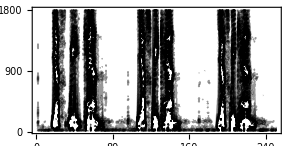

```mathematica
ListContourPlot[Transpose@Table[Abs[Fourier[data⟦n;;n+1600-1⟧]]⟦1;;120⟧,{n,900000,900000+1600*250,1600}],Contours->20,ContourShading->None,ImageSize->{500,300},AspectRatio->0.5,Ticks->{None,None},
FrameTicks->{Automatic,Function[{min,max},Table[{i,i*15},{i,0,max,20}]]}]
```

Tweaking the Contours and ContourShading options prevent the white-outs in the peak regions.

```mathematica
ListContourPlot[Transpose@Table[Abs[Fourier[data⟦n;;n+1600-1⟧]]⟦1;;120⟧,{n,900000,900000+1600*250,1600}],Contours->Function[{min,max},Range[0,max,0.25]],ContourShading->Table[GrayLevel[1-n/16.],{n,16}],PlotRange->All,
ImageSize->{800,400},AspectRatio->0.5]
```

-Graphics-

A Spectrograph

ArrayPlot is another perfect tool to display the results. ArrayPlot will automatically scale the results such that the greater the energy content in the frequency domain, the darker the plot. Frequency runs across the page, as shown previously in Recipe 9.17, whereas the individual slices run down the page.

```mathematica
SetOptions[ArrayPlot,ImageSize->{600,200},AspectRatio->0.25];
```

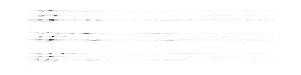

```mathematica
ArrayPlot[Table[Abs[Fourier[data⟦n;;n+1600-1⟧]]⟦1;;100⟧,{n,900000,900000+1600*250,1600}],FrameTicks->{Automatic,Table[{n,30*n},{n,0,100,5}]}]
```

You can improve on ArrayPlot’s formatting. Convention wants time to run left to right across the page and frequency to run bottom to top. Transpose will reverse the axes, but you’ll also need DataReversed→True to make time run left to right.

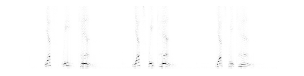

```mathematica
ArrayPlot[Transpose@Table[Abs[Fourier[data⟦n;;n+1600-1⟧]]⟦1;;120⟧,{n,900000,900000+1600*250,1600}],FrameTicks->{Table[{n,30*n},{n,0,100,10}],Table[{n,0.03333*n//Round},{n,0,250,30}]},DataReversed->True]
```

You could set a threshold and display in black and white.

```mathematica
ArrayPlot[Transpose@Table[Abs[Fourier[data⟦n;;n+1600-1⟧]]⟦1;;120⟧,{n,900000,900000+1600*250,1600}]/.{_Real?(#>=0.3 &):>1,_Real?(#<0.3 &):>0},
```

```mathematica
FrameTicks->{Table[{n,30*n},{n,0,100,10}],Table[{n,0.03333*n//Round},{n,0,250,30}]},DataReversed->True]
```

-Graphics-

Or, you could zoom in and look more closely at the lower frequencies.

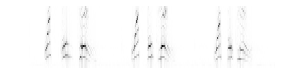

```mathematica
ArrayPlot[Transpose@Table[Abs[Fourier[data⟦n;;n+1600-1⟧]]⟦1;;30⟧,{n,900000,900000+1600*250,1600}],FrameTicks->{Table[{n,30*n},{n,0,30,5}],Table[{n,0.03333*n//Round},{n,0,250,30}]},DataReversed->True]
```